## 基本的な数学用コマンド

### ベクトルと行列の演算

```mathematica
ベクトル同士の加減は直接+-を使う
```

```mathematica
{1,2,3}+{1,0,5}
{1,2,3}-{1,0,5}
```

```mathematica
問題　　平均0，分散1の正規分布に従う乱数を50個つくりなさい．50個の乱数を含むリストを2つ作り，リスト同士を足した結果と引いた結果を示せ
```

```mathematica
問題　　前問を使って，平均が異なる正規乱数リストの引き算の結果を示せ．
```

#### ベクトルの内積

```mathematica
{a,b,c} . {x,y,z}
```

```mathematica
{1,2,3}.{10,0,5}
```

```mathematica
(* 内積は，行列の掛け算の特殊例である *)
```

#### 行列の掛け算

```mathematica
m={{1,2,3},{4,2,2},{5,1,7}};
m2={{1,0,0},{0,1,0},{0,0,1}};
```

```mathematica
m.m2
```

```mathematica
Inverse[m].m
```

### 代数式の簡略化

```mathematica
面倒なだけの初等計算はコンピュータにまかせる
```

```mathematica
Expand[((y+3)^3)(x+3)^5]
```

6561+10935 x+7290 x^2+2430 x^3+405 x^4+27 x^5+6561 y+10935 x y+7290 x^2 y+2430 x^3 y+405 x^4 y+27 x^5 y+2187 y^2+3645 x y^2+2430 x^2 y^2+810 x^3 y^2+135 x^4 y^2+9 x^5 y^2+243 y^3+405 x y^3+270 x^2 y^3+90 x^3 y^3+15 x^4 y^3+x^5 y^3

```mathematica
一見複雑な式も，Simplifyで簡略化してくれる
直前の出力を参照するには%を使う．
```

```mathematica
Simplify[%]
```

```mathematica
Expand[]や　Simplify[]　Factor[ ]は組み込み関数である．
組み込み関数のヘルプにはコマンドを反転選択した後，ファンクションキー1(F1)をおす
```

```mathematica
練習  (x+y)を100乗せよ
```

```mathematica
問題　次の式を簡略化せよ
1+4 x+6 x^2+4 x^3+x^4+12 y+36 x y+36 x^2 y+12 x^3 y+54 y^2+108 x y^2+54 x^2 y^2+108 y^3+108 x y^3+81 y^4
```

### 関数のPlot

```mathematica
関数x^2を[-4,4]の範囲でプロットする
```

```mathematica
Plot[x^2,{x,-4,4}]
```

```mathematica
問題　x^3のグラフをプロットせよ．適切な範囲を考えよ
```

```mathematica
{}を用いて関数をリストにすれば，複数の関数を同時にプロットできる
これは関数を比較する際によく用いる
```

```mathematica
Plot[{x^2,x^3},{x,-4,4}]
```

```mathematica
色を指定するにはPlotStyleで順番に指定する
```

```mathematica
Plot[{Sin[x^2], Cos[x^2]},{x,0,3},PlotStyle->{Red,Blue}]
```

```mathematica
問題　　ヘルプでPlotStyleを調べて，x^3の《赤色で太い線のグラフ》を描け
```

```mathematica
線の形式や太さも自由に選べる．このようにグラフィックを簡単に制御できる点がMathematicaのメリットである
```

```mathematica
Plot[{Sin[x^2], Cos[x^2]},{x,0,3},PlotStyle->{{Red,Thick},{Blue,Dashed}}]
```

```mathematica
PlotRange を使い y の区間を指定する．y の極限をこのように指定すると，曲線の下の部分は表示されなくなる．
```

```mathematica
Plot[Sin[x^2],{x,0,3},PlotRange->{0,1.2}]
```

### 微分と積分

```mathematica
xについての導関数
```

```mathematica
D[x^n,x]
```

n x^(-1+n)

```mathematica
xについての4次導関数：
```

```mathematica
D[Sin[x]^10,{x,4}]
```

5040 Cos[x]^4 Sin[x]^6-4680 Cos[x]^2 Sin[x]^8+280 Sin[x]^10

```mathematica
問題　関数　Exp[x]の5次導関数をもとめよ
```

```mathematica
問題　ヘルプで関数　Seriesを検索せよ

次の関数を第10項までマクローリン展開せよ
Exp[x^2]
```

```mathematica
問題　　Exp[x]とこれをマクローリン展開で近似した関数を同時Plotにより比較せよ
```

```mathematica
不定積分
```

```mathematica
Integrate[2 x,x]
Integrate[1/x,x]
```

x^2

Log[x]

```mathematica
定積分
```

```mathematica
Integrate[2 x,{x,1,2}]
```

3

```mathematica
定積分の直感的意味は，面積を求めることである
```

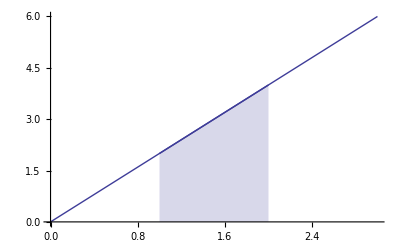

```mathematica
Show[Plot[2 x,{x,0,3},PlotRange->{0,6}],Plot[2 x,{x,1,2},PlotRange->{0,6},Filling->Bottom]]
```

### 代数方程式を解く

```mathematica
2次方程式を解く
```

```mathematica
Solve[x^2+2 x+1==0,x]
```

```mathematica
連立方程式をxとyについて解く
```

```mathematica
Solve[{a x+y==7,b x-y==1},{x,y}]
```

```mathematica
代入リストを利用して，解だけを出力する
```

```mathematica
x/.{x->3}
```

```mathematica
sol=Solve[{x^2+y^2==1,x+y==1},{x,y}];
x/.sol
```

### 微分方程式を解く

```mathematica
微分方程式を解く
```

```mathematica
DSolve[y'[x]+y[x]==Sin[x],y[x],x]
```

```mathematica
初期条件を指定する
```

```mathematica
DSolve[{y'[x]+y[x]==Sin[x],y[0]==0},y[x],x]
```

### 棒グラフ

```mathematica
高さのリストの棒グラフを生成する
```

```mathematica
BarChart[{1,2,3}]
```

```mathematica
カテゴリ的なラベルを使う
```

```mathematica
BarChart[{{1,2,3},{1,3,2},{5,2}},ChartLabels->{"a","b","c"}]
```

```mathematica
(*  お好みでMac風に  *)
BarChart[{5,4,2,3,6},ChartElementFunction->"GlassRectangle"]
```